```mathematica
Grow[list_]:=Table[list⟦;;i⟧,{i,Length[list]}];
Whither[list_] :=Table[list⟦i;;⟧,{i,Length[list]}];
```

```mathematica
borderCircleCenters[{x_,y_},r_] := Table[{x+r Cos[i 2Pi/6],y+r Sin[i 2Pi/6]},{i,0,5}];
getAllCenters[r_]:=Module[{centers,borderCenters, searchR,ord,rt},
ord[{a_,b_},{c_,d_}]:= If[a<c,True,b<d];
centers={{0,0}};

rt=Power[r,1/2];
While[Norm[centers⟦-1⟧]≤Min[2,1+rt],
borderCenters=Map[borderCircleCenters[#,r]&,centers];
centers = centers ∪Flatten[borderCenters,1]];

Sort[Select[centers,Norm[#]<1+r&],ord]
];

Timing[allCenters=Table[getAllCenters[1/2^n],{n,0,5}];]
```

{58.6677,Null}

```mathematica
makeCircle[center_,r_]:={Thickness[r*0.01],Circle[center,r]};
centersToCircles[centers_,r_]:=Map[makeCircle[#,r]&,centers];
plotCircles[centers_,r_]:= Graphics[centersToCircles[centers,r],ImagePadding->5,PlotRange->{{-1,1},{-1,1}}, ImageSize->{400,400}];
```

```mathematica
Apply[Plus,Table[Length[allCenters⟦i⟧],{i,0,Length[allCenters]}]]
```

5406

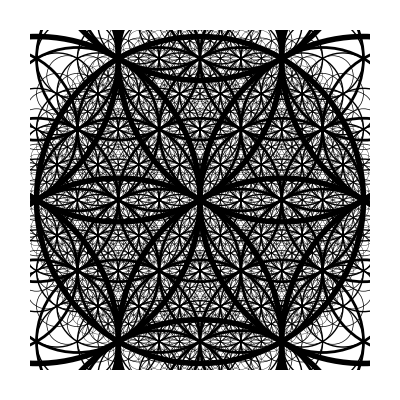

```mathematica
layers=Table[plotCircles[allCenters⟦i+1⟧,1/2^i],{i,0,4}];
Show[layers]
```

```mathematica
indexedCenters = Flatten[allCenters,1];
```

```mathematica
(* extracts a pair {center, radius} given the index of the circle *)
indexToCenterRadius[layeredCenters_,index_]:=Module[{row,length,counter},
row=1;
length=Length[layeredCenters⟦row⟧];
counter=index;

While[counter > length,
counter -= length;
row++;
length = Length[layeredCenters⟦row⟧];
];

{layeredCenters⟦row,counter⟧,1/2^(row-1)}
];
```

```mathematica
drawArc[{index_,thickness_,arcStart_,arcEnd_}]:= Module[{center,radius},
{center,radius}=indexToCenterRadius[allCenters, index];
Graphics[{Thickness[thickness],Circle[center,radius,{arcStart,arcEnd}]},ImagePadding->5,PlotRange->{{-1,1},{-1,1}}, ImageSize->{400,400}]
];
drawCircle[index_,thickness_]:=drawArc[index,thickness,0,2Pi]
```

```mathematica
(*
indexFrames = Table[drawCircle[i,0.005],{i,1,129}];
Export["index-animation.gif",Map[Show,Grow[indexFrames]],"DisplayDurations"->0.25]
*)
```

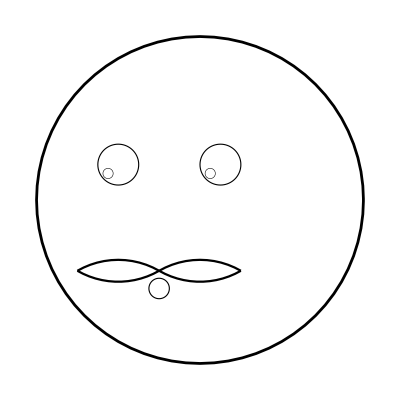

```mathematica
paint[coordinates_]:=Show[Map[drawArc,coordinates]];
smiley={{7,0.005,0,2Pi},{197,0.002,0,2Pi},{299,0.002,0,2Pi},{783,0.002,0,2Pi},{2140,0.001,0,2Pi},{3592,0.001,0,2Pi},{22,0.004,8Pi/6,10Pi/6},{29,0.004,4Pi/3,5Pi/3},
{21,0.004,Pi/3,2Pi/3},{28,0.004, Pi/3,2Pi/3}};
paint[smiley]
```

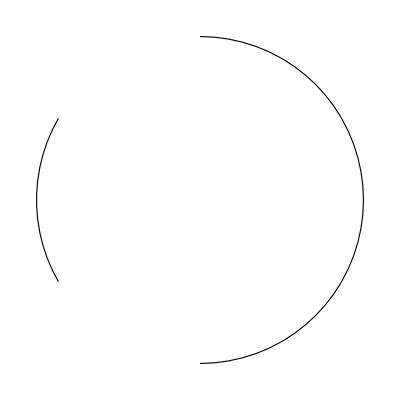

```mathematica
paint[{{7,0.002,Pi-Pi/6,Pi+Pi/6},{7,0.002,-Pi/2,Pi/2}}]
```